```mathematica
ClearAll["Global`*"]
```

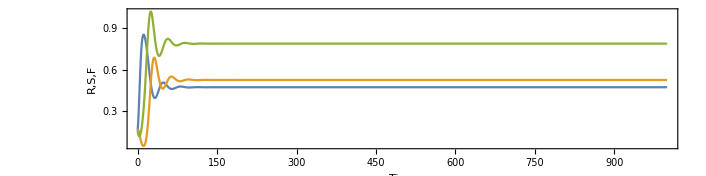

```mathematica
MetapopDyn[a_,λ_,σ_,ρ_,m_,μ_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -(ρ*X[t] + m*Y[t])*R[t] ,
X'[t] ==σ*(1-R[t])*Y[t] - ρ* R[t]*X[t] - μ*X[t],
Y'[t] ==λ*Y[t]-σ*(1-R[t])*Y[t] +ρ* R[t] * X[t],
R[0]==0.16,X[0]==0.16,Y[0]==0.16},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=0.5,λ=0.2,σ=0.5,ρ=0.2,m=0.2,μ=0.3,T=1000},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,λ,σ,ρ,m,μ,T] ];
Plot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","R,S,F"}]
]
```

The below code solves for the steady state

```mathematica
Sol =FullSimplify[Solve[{
0 == α*R*(1-R)-R*(ρ*H+m*F),
0==σ*(1-R)*F-ρ*R*H-μ*H, 
0==λ*F-σ*(1-R)*F+ρ*R*H},
{R,H,F}]]
```

{{R→0,H→0,F→0},{R→1,H→0,F→0},{R→(μ (-λ+σ))/(λ ρ+μ σ),H→(α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ)),F→(α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))}}

```mathematica
InternalSol1 = Sol[[3]];
(*InternalSol2 = Sol[[4]];*)
```

```mathematica
{InternalSol1}/.{α->0.5,λ->0.1,μ->0.2,ρ->0.5,σ->0.5, m->0.2}
```

{{R→0.533333,H→0.259259,F→0.518519}}

This means only InternalSol2 is an INTERNAL, POSITIVE SOLUTION

```mathematica
IntPosSol = InternalSol1;
```

```mathematica
Rstar = IntPosSol[[1]][[2]]
Hstar = IntPosSol[[2]][[2]]
Fstar = IntPosSol[[3]][[2]]
```

(μ (-λ+σ))/(λ ρ+μ σ)

(α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))

(α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))

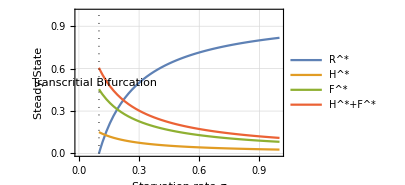

```mathematica
With[{alpha=0.5,lambda=0.1,mu=0.3,rho=0.3,mr=1},
Rstarspec = IntPosSol[[1]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho,m->mr};
Xstarspec = IntPosSol[[2]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho,m->mr};
Ystarspec = IntPosSol[[3]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho,m->mr};
FigFP=
Show[{
Plot[{Rstarspec,Xstarspec,Ystarspec,Xstarspec+Ystarspec},{σ,lambda,1},PlotTheme->"Detailed",FrameLabel->{"Starvation rate σ","Steady State"},PlotRange->{{0,1},{0,1}},ImageSize->300,PlotLegends->{"R^*","H^*","F^*","H^*+F^*"}],
Graphics[{Dotted,Line[{{lambda,0},{lambda,1}}]}],
Graphics[Rotate[Text["Transcritial Bifurcation",{(lambda-0.02),0.5}],90Degree]]
}]
]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/Manuscript/fig_FP.pdf",FigFP]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/Manuscript/fig_FP.pdf

```mathematica
Limit[{Rstarspec,Xstarspec,Ystarspec},σ->Infinity]
```

{1.,0.,0.}

```mathematica
dR=   α*R*(1-R)-R*(ρ*H+m*F);
dX =σ*(1-R)*F-ρ*R*H-μ*H;
dY =λ*F-σ*(1-R)*F+ρ*R*H;
JacSpec = {
{D[dR,R],D[dR,H],D[dR,F]},
{D[dX,R],D[dX,H],D[dX,F]},
{D[dY,R],D[dY,H],D[dY,F]}
}
```

{{-F m+(1-R) α-R α-H ρ,-R ρ,-m R},{-H ρ-F σ,-μ-R ρ,(1-R) σ},{H ρ+F σ,R ρ,λ-(1-R) σ}}

```mathematica
JacSpec//MatrixForm
```

(-F m+(1-R) α-R α-H ρ | -R ρ | -m R
-H ρ-F σ | -μ-R ρ | (1-R) σ
H ρ+F σ | R ρ | λ-(1-R) σ)

```mathematica
JacSpecSol = JacSpec/.{R->Rstar,H->Hstar,F->Fstar};
```

```mathematica
JacSpecSol
```

{{-(m α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))-(α λ^2 ρ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))-(α μ (-λ+σ))/(λ ρ+μ σ)+α (1-(μ (-λ+σ))/(λ ρ+μ σ)),-(μ ρ (-λ+σ))/(λ ρ+μ σ),-(m μ (-λ+σ))/(λ ρ+μ σ)},{-(α λ^2 ρ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))-(α λ μ (μ+ρ) σ)/((m μ+λ ρ) (λ ρ+μ σ)),-μ-(μ ρ (-λ+σ))/(λ ρ+μ σ),σ (1-(μ (-λ+σ))/(λ ρ+μ σ))},{(α λ^2 ρ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))+(α λ μ (μ+ρ) σ)/((m μ+λ ρ) (λ ρ+μ σ)),(μ ρ (-λ+σ))/(λ ρ+μ σ),λ-σ (1-(μ (-λ+σ))/(λ ρ+μ σ))}}

```mathematica
({R,H,F}/.Sol)/.{α->alpha,λ->lambda,μ->mu,ρ->rho,σ->sigma,m->mr}
```

{{0,0,0},{1,0,0},{(mu (-lambda+sigma))/(lambda rho+mu sigma),(alpha lambda^2 (mu+rho))/((mr mu+lambda rho) (lambda rho+mu sigma)),(alpha lambda mu (mu+rho))/((mr mu+lambda rho) (lambda rho+mu sigma))}}

This plot shows that the bifurcation at lambda=sigma is a Transcritical (I think)

```mathematica
({R,H,F}/.Sol)/.{α->0.5,λ->0.1,μ->0.2,ρ->0.2,m->0.2,σ->sigma}
```

{{0,0,0},{1,0,0},{(0.2 (-0.1+sigma))/(0.02+0.2 sigma),0.0333333/(0.02+0.2 sigma),0.0666667/(0.02+0.2 sigma)}}

```mathematica
Manipulate[
Eig = Eigenvalues[JacSpecSol/.{α->0.5,λ->0.1,μ->0.2,ρ->0.2,m->0.2,σ->sigma}];
REig = Re[Eig];
IEig = Im[Eig];
Row[{
Show[{
ListPlot[Transpose[{REig,IEig}],PlotRange->{{-1,1},{-1,1}}],
Graphics[{LightGray,Opacity[0.3],Disk[]}]
},ImageSize->300,Frame->True,AspectRatio->1,FrameLabel->{"Real part","Imaginary part"}],
FP=({R,H,F}/.Sol)/.{α->0.5,λ->0.1,μ->0.2,ρ->0.2,m->0.2,σ->sigma};
Show[{
ListPointPlot3D[FP,
PlotStyle->Directive[{ColorData[97,4],PointSize[Large]}],PlotLabel->FP,PlotRange->{{-1,1},{0,1},{0,1}},ImageSize->300,AxesLabel->{"R^*","S^*","F^*"}],
Graphics3D[{Opacity[0.5],Polygon[{{0,0,0},{0,1,0},{0,1,1},{0,0,1}}]}]
}]
}],
{{sigma,0.1},0,1,0.001}]
```

```mathematica
FP
```

{{0,0,0},{1,0,0},{0.,0.166667,0.333333}}

Specific Bifurcations

```mathematica
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,μ]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,α]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,ρ]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,λ]
```

{{σ→λ}}

{{μ→0},{μ→-ρ}}

{{α→0}}

{{ρ→-μ}}

{{λ→0},{λ→σ}}

```mathematica
SylvesterMatrix=Function[{Jac},
Dim = Length[Jac];
Mat = Table[0,{Dim-1},{Dim-1}];
Col1 = Table[Subscript[ℼ,i],{i,1,(Dim-1)*2,2}];
Mat[[All,1]] = Col1;
Table[
Mat[[i]][[j]] = Subscript[ℼ,Mat[[i]][[j-1]][[2]]-1];
,{j,2,Dim-1},{i,1,Dim-1,1}];
Todel=Select[Flatten[Mat],#[[2]]<0||#[[2]]>(Dim)&];
Mat=Mat/.Table[Todel[[i]]->0,{i,1,Length[Todel],1}];
CPG = FullSimplify[CharacteristicPolynomial[Jac,λ]];
CPGL = CoefficientList[CPG,λ];
Mat2 = Mat/.Table[Subscript[ℼ,i]-> CPGL[[i+1]],{i,0,(Length[CPGL]-1),1}]
];
```

```mathematica
Sylv=SylvesterMatrix[JacSpecSol];
HopfSol=Solve[Det[Sylv]==0,muy];
```

$Aborted

```mathematica
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
```

```mathematica
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
```

```mathematica
HopfAnalytic = Solve[Det[Sylv]==0,ρ];
```

```mathematica
HopfAnalytic
```

{{ρ→-(m λ^2-λ^3+m λ μ-α λ μ-m λ σ+2 λ^2 σ-m μ σ+α μ σ+4 λ μ σ+2 μ^2 σ-λ σ^2-μ σ^2)/(4 (λ+μ) σ)-1/2 √1-1/2 √(((m λ^2-λ^3+m λ μ-α λ μ-m λ σ+2 λ^2 σ-m μ σ+α μ σ+4 λ μ σ+2 μ^2 σ-λ σ^2-μ σ^2)^2)/(2 (λ+μ)^2 σ^2)-(m α λ^3 μ-α λ^4 μ+m λ^3 μ^2-α λ^3 μ^2-m α λ^2 μ σ+2 m λ^3 μ σ+2 α λ^3 μ σ+2 4+α λ^2 1 σ+3 λ^3 μ^2 σ+λ^2 μ^3 σ-2 m λ^2 μ σ^2-α λ^2 μ σ^2-3 m λ μ^2 σ^2-m μ^3 σ^2)/(λ^2 (λ+μ) σ)-(m α λ^4 μ-α λ^5 μ+29+m μ^3 σ^3)/(3 (λ^4 σ+1-1-λ^2 μ σ^2))-1/1-(1)^(1/3)/(3 2^(1/3) λ^2 (λ+μ) (λ σ-σ^2))-(-(8 (2 m α λ^2 μ^2+m λ^3 μ^2+m α λ μ^3+3 m λ^2 μ^3-2 m α λ μ^2 σ-m λ^2 μ^2 σ-m α μ^3 σ-3 m λ μ^3 σ+λ^2 μ^3 σ-2 m μ^4 σ))/(λ^2 (λ+μ))-((m λ^2-λ^3+m λ μ-α λ μ-m λ σ+1-1+α μ σ+4 λ μ σ+2 μ^2 σ-λ σ^2-μ σ^2)^3)/((λ+μ)^3 σ^3)+1/(λ^2 (λ+μ)^2 σ^2)4 (m λ^2-λ^3+m λ μ-α λ μ-m λ σ+2 λ^2 σ-m μ σ+α μ σ+4 λ μ σ+2 μ^2 σ-λ σ^2-μ σ^2) (m α λ^3 μ-α λ^4 μ+m λ^3 μ^2-α λ^3 μ^2-m α λ^2 μ σ+2 m λ^3 μ σ+2 α λ^3 μ σ+2 m λ^2 μ^2 σ+α λ^2 μ^2 σ+3 λ^3 μ^2 σ+λ^2 μ^3 σ-2 m λ^2 μ σ^2-α λ^2 μ σ^2-3 m λ μ^2 σ^2-m μ^3 σ^2))/(4 √(((m λ^2-λ^3+m λ μ-α λ μ-m λ σ+2 λ^2 σ-m μ σ+α μ σ+4 λ μ σ+2 μ^2 σ-λ σ^2-μ σ^2)^2)/(4 (λ+μ)^2 σ^2)-(m α λ^3 μ-α λ^4 μ+m λ^3 μ^2-α λ^3 μ^2-m α λ^2 μ σ+2 m λ^3 μ σ+2 α λ^3 μ σ+2 m λ^2 μ^2 σ+α λ^2 μ^2 σ+3 λ^3 μ^2 σ+λ^2 μ^3 σ-2 m λ^2 μ σ^2-α λ^2 μ σ^2-3 m λ μ^2 σ^2-m μ^3 σ^2)/(λ^2 (λ+μ) σ)+(m α λ^4 μ-α λ^5 μ+28+3 m λ μ^2 σ^3+m μ^3 σ^3)/(3 (λ^4 σ+λ^3 μ σ-λ^3 σ^2-λ^2 μ σ^2))+(2^(1/3) 2 ((m α λ^4 μ-α λ^5 μ+28+3 m λ μ^2 σ^3+m μ^3 σ^3)^2-1+12 (λ^4 σ+λ^3 μ σ-1-λ^2 μ σ^2) (m α λ^3 μ^3 σ+8+m α μ^4 σ^3+m μ^5 σ^3)))/(3 λ^2 (λ+μ) (λ σ-σ^2)^2 (7+√(-4 1^3+1^2))^(1/3))+((7+√(-4 (1)^3+(1)^2))^(1/3))/(3 2^(1/3) λ^2 (λ+μ) (λ σ-σ^2)))))},{ρ→1},1,{ρ→1}}
 |  |  |  |

```mathematica
FullSimplify[HopfAnalytic]
```

$Aborted

The solution to the Hopf Bifurcation surface may not be analytically tractable
Try Solving numerically with a = 1

```mathematica
Hsp = HopfAnalytic/.{α->0.5,μ->0.2,m->MR,λ->0.2};
curves = Table[ρ/.Hsp[[4]],{MR,0.1,1,0.1}];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

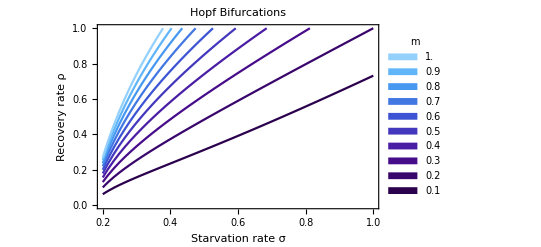

```mathematica
HopfPlot = Plot[curves,{σ,0.2,1},PlotRange->{0,1},Frame->True,FrameLabel->{"Starvation rate σ","Recovery rate ρ"},PlotStyle->ColorData["DeepSeaColors"]/@(Range[0,Length@curves]/Length@curves),PlotLegends->SwatchLegend[ Table[MR,{MR,0.1,1,0.1}],LegendLayout->{"ReversedColumn",1},LegendLabel->"m"],PlotLabel->"Hopf Bifurcations"]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/figs/HopfPlot_sig_rho_m.pdf",HopfPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/figs/HopfPlot_sig_rho_m.pdf

```mathematica
ColorData[35,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Hsp
```

{{λ→σ},{λ→Root[0.000576 σ^2+(-0.00032 σ+0.00432 σ^2) #1+(-0.00576 σ+0.0088 σ^2) #1^2+(0.00016-0.024 σ+0.008 σ^2) #1^3+(0.0024-0.016 σ) #1^4+0.008 #1^5&,1]},{λ→Root[0.000576 σ^2+(-0.00032 σ+0.00432 σ^2) #1+(-0.00576 σ+0.0088 σ^2) #1^2+(0.00016-0.024 σ+0.008 σ^2) #1^3+(0.0024-0.016 σ) #1^4+0.008 #1^5&,2]},{λ→Root[0.000576 σ^2+(-0.00032 σ+0.00432 σ^2) #1+(-0.00576 σ+0.0088 σ^2) #1^2+(0.00016-0.024 σ+0.008 σ^2) #1^3+(0.0024-0.016 σ) #1^4+0.008 #1^5&,3]},{λ→Root[0.000576 σ^2+(-0.00032 σ+0.00432 σ^2) #1+(-0.00576 σ+0.0088 σ^2) #1^2+(0.00016-0.024 σ+0.008 σ^2) #1^3+(0.0024-0.016 σ) #1^4+0.008 #1^5&,4]},{λ→Root[0.000576 σ^2+(-0.00032 σ+0.00432 σ^2) #1+(-0.00576 σ+0.0088 σ^2) #1^2+(0.00016-0.024 σ+0.008 σ^2) #1^3+(0.0024-0.016 σ) #1^4+0.008 #1^5&,5]}}

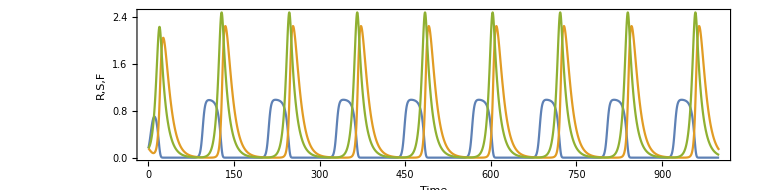

```mathematica
MetapopDyn[a_,λ_,σ_,ρ_,m_,μ_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -(ρ*X[t] + m*Y[t])*R[t] ,
X'[t] ==σ*(1-R[t])*Y[t] - ρ* R[t]*X[t] - μ*X[t],
Y'[t] ==λ*Y[t]-σ*(1-R[t])*Y[t] +ρ* R[t] * X[t],
R[0]==0.16,X[0]==0.16,Y[0]==0.16},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=0.5,λ=0.2,σ=0.3,ρ=0.8,m=0.1,μ=0.2,T=1000},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,λ,σ,ρ,m,μ,T] ];
Plot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","R,S,F"}]
]
```

```mathematica
ParallelTable[
Hsp2 =HopfAnalytic/.{α->0.5,μ->0.2,m->MR};
Plot3D[ρ/.Hsp2[[4]],{σ,0,1},{λ,0,1},PlotRange->{0,1}, RegionFunction->Function[{x,y,z},x>y],
ClippingStyle->None,PlotStyle->{Directive[ColorData[97,1],Opacity[0.8]],Directive[ColorData[97,1],Opacity[0.8]]},Mesh->5,AxesLabel->{"σ","λ","ρ"},Lighting->{{"Ambient", White}}],{MR,{0.2,1}}]
```

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0.\ 2^1/3\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^1/3 encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ 2^1/3\ ComplexInfinity\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ 2^1/3\ ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity/2^1/3 encountered.

Infinity::indet: Indeterminate expression 0.\ 2^1/3\ ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.\ 2^1/3\ ComplexInfinity\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{-Graphics3D-,-Graphics3D-}

```mathematica
Hsp3 = HopfAnalytic/.{α->0.5,μ->0.2,λ->0.1};
Plot3D[ρ/.Hsp3[[4]],{σ,0,1},{m,0,2}]
```

-Graphics3D-

```mathematica
HopfData = Table[{σ,Re[N[λ/.Hsp[[4]]]]},{σ,0.1,1,0.01}];
(*HopfData=Join[{Reverse[HopfNumSol2down,2]/.σ->"NA",Reverse[HopfNumSol2up,2]/.σ->"NA"}];*)
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/HopfData.csv",HopfData,"CSV"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/HopfData.csv

```mathematica
Hsp2LS = Hsp2[[4]]/.σ->λ;
```

```mathematica
co2NUM  = Table[NSolve[λ/.Hsp2LS,μ],{λ,0.1,1,0.1}]
```

$Aborted

```mathematica
PS = λ/.Hsp2LS;
NSolve[0.5==PS/.λ->0.5,μ]
```

{}

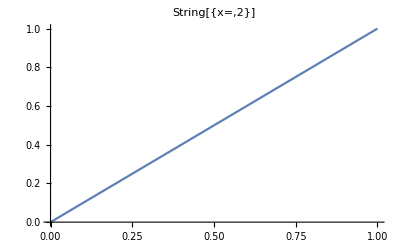

```mathematica
Plot[x,{x,0,1},PlotLabel->String[{"x=",2}]]
```

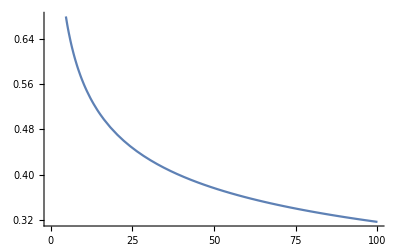

```mathematica
Plot[x^(0.75-1),{x,0,100}]
```